# Problema 22

## Apartat (a)

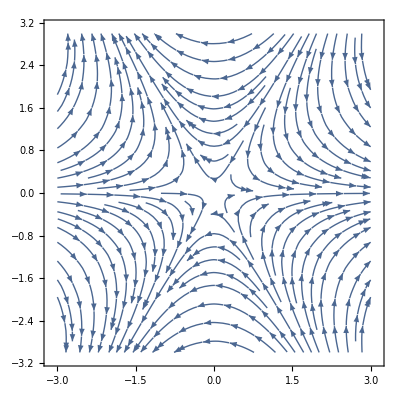

```mathematica
StreamPlot[{3(x^2-y^2),-6(x*y)},{x,-3,3},{y,-3,3}]
```

## Apartat (b)

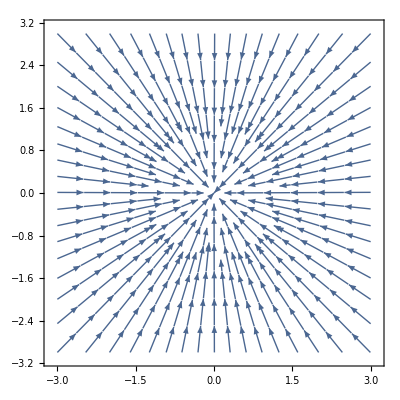

```mathematica
field={-1/(2*Pi*r),0};
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",field,{r,θ}->{x,y}],{x,-3,3},{y,-3,3}]
```

## Apartat (d)

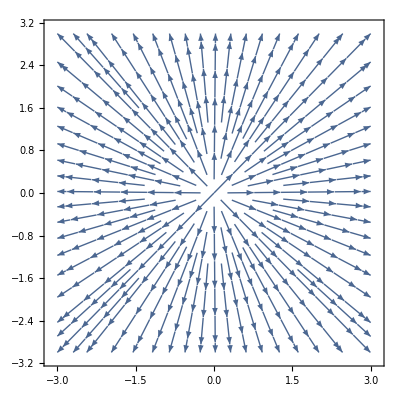

```mathematica
StreamPlot[{x,y},{x,-3,3},{y,-3,3}](*NO EXISTEIX STREAMLINE*)
```

## Apartat (c)

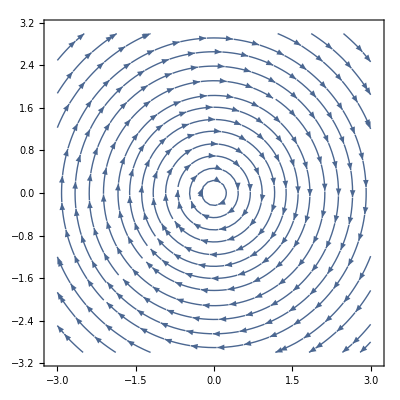

```mathematica
field={0,-1/(2*Pi*r)};(*NO ROTACIONAL*)
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",field,{r,θ}->{x,y}],{x,-3,3},{y,-3,3}]
```

## Apartat (f)

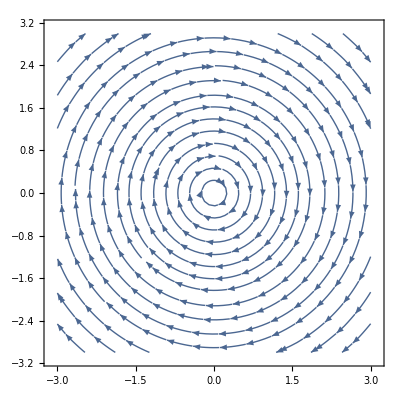

```mathematica
StreamPlot[{y,-x},{x,-3,3},{y,-3,3}](*ROTACIONAL*)
```

## Apartat (e)

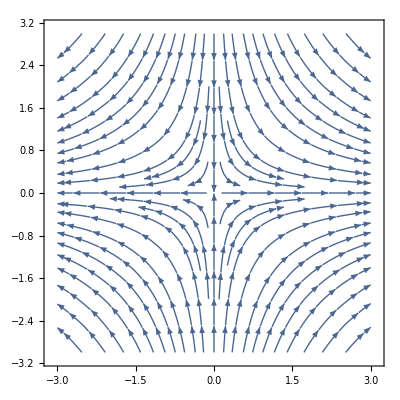

```mathematica
StreamPlot[{x,-y},{x,-3,3},{y,-3,3}]
```

## Apartat (g)

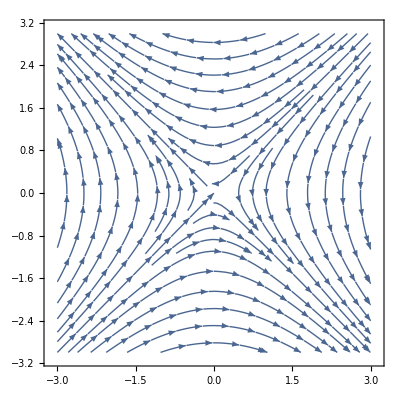

```mathematica
StreamPlot[-{y,x},{x,-3,3},{y,-3,3}]
```